```mathematica
<<MASStoolbox`
<<XML`
SetDirectory[NotebookDirectory[]];
SetDirectory[".."];
<<util`
```

# SB2 Systems Biology: Simulation of Dynamic Network States

## PPP

### Construct model

```mathematica
SetDirectory[NotebookDirectory[]];
glycolysis=Import["../../models/SB2/glycolysis.m.gz"];
```

```mathematica
chemicalFormulas={g6p^c->"H11C6O9P",f6p^c->"H11C6O9P",gap^c->"H5C3O6P",fbp^c->"H10C6O12P2",gl6p^c->"H9C6O9P",go6p^c->"H10C6O10P",ru5p^c->"H9C5O8P",x5p^c->"H9C5O8P",r5p^c->"H9C5O8P",s7p^c->"H13C7O10P",e4p^c->"H7C4O7P",nadp^c->"&NADP&",nadph^c->"H&NADP&",gsh^c->"H17C10N3O6S",gssg^c->"H32C20N6O12S2",co2^c->"CO2",h2o^c->"H2O",h^c->"H"};
rxns={Overscript[g6p^c+nadp^c⇌gl6p^c+h^c+nadph^c, vg6pdh],Overscript[gl6p^c+h2o^c⇌go6p^c+h^c, vpglase],Overscript[go6p^c+nadp^c⇌co2^c+nadph^c+ru5p^c, vgl6pdh],Overscript[ru5p^c⇌x5p^c, vr5pe],Overscript[ru5p^c⇌r5p^c, vr5pi],Overscript[r5p^c+x5p^c⇌gap^c+s7p^c, vtki],Overscript[e4p^c+x5p^c⇌f6p^c+gap^c, vtkii],Overscript[gap^c+s7p^c⇌e4p^c+f6p^c, vtala],Overscript[gssg^c+h^c+nadph^c⇌2 gsh^c+nadp^c, vgssgr],Overscript[2 gsh^c⇌gssg^c+2 h^c, vgshr],(co2^c⇌∅)^vco2,(g6p^c⇌∅)^EX_g6p_c,(f6p^c⇌∅)^EX_f6p_c,(r5p^c⇌∅)^EX_r5p_c,(h^c⇌∅)^EX_h_c,(h2o^c⇌∅)^EX_h2o_c,(gap^c⇌∅)^EX_gap_c};
(*ststConcentrations=#[[1]]->#[[2]]Milli Mole Liter^-1&/@{g6p^c->0.0486,f6p^c->0.0198,gap^c->0.00728,gl6p^c->0.001754242723,go6p^c->0.037475258,ru5p^c->0.0049367903,x5p^c->0.014784196,r5p^c->0.00494,s7p^c->0.023987984,e4p^c->0.0050750696,nadp^c->0.0002,nadph^c->0.0658,gsh^c->3.2,gssg^c->0.11999999999999966,h^c->0.0000714957344480193,h2o^c->0.99999683,co2^c->1.0000021};*)
ststConcentrations={g6p^c->0.0486 Millimole Liter^-1,f6p^c->0.0198 Millimole Liter^-1,gap^c->0.00728 Millimole Liter^-1,gl6p^c->0.001754242723 Millimole Liter^-1,go6p^c->0.037475258 Millimole Liter^-1,ru5p^c->0.0049367903 Millimole Liter^-1,x5p^c->0.014784196 Millimole Liter^-1,r5p^c->0.012668936 Millimole Liter^-1,s7p^c->0.023987984 Millimole Liter^-1,e4p^c->0.0050750696 Millimole Liter^-1,nadp^c->0.0002 Millimole Liter^-1,nadph^c->0.0658 Millimole Liter^-1,gsh^c->3.2 Millimole Liter^-1,gssg^c->0.11999999999999966 Millimole Liter^-1,co2^c->1.0000021 Millimole Liter^-1,h^c->0.0000714957344480193 Millimole Liter^-1,h2o^c->0.9999979 Millimole Liter^-1};
eqConstants={Underscript[K, EX_r5p_c]->∞,Underscript[K, EX_h_c]->1,Underscript[K, EX_h2o_c]->1,Underscript[K, EX_g6p_c]->1,Underscript[K, EX_gap_c]->∞,Underscript[K, EX_f6p_c]->∞,Underscript[K, vg6pdh]->1000,Underscript[K, vpglase]->1000,Underscript[K, vgl6pdh]->Mole Liter^-1,Underscript[K, vr5pe]->3,Underscript[K, vr5pi]->2.57,Underscript[K, vtki]->1.2,Underscript[K, vtkii]->10.3,Underscript[K, vtala]->1.05,Underscript[K, vgssgr]->1/10 Mole Liter^-1,Underscript[K, vgshr]->2000 Liter Mole^-1,Underscript[K, vco2]->1};
(*eqConstantsBook={Underscript[K, vg6pdh]->1000,Underscript[K, vpglase]->1000,Underscript[K, vgl6pdh]->1000,Underscript[K, vr5pe]->3,Underscript[K, vr5pi]->2.57,Underscript[K, vtki]->1.2,Underscript[K, vtkii]->10.3,Underscript[K, vtala]->1.05,Underscript[K, vgssgr]->100,Underscript[K, vgshr]->2,Underscript[K, vco2]->1};*)
externalConcentrations={h^Xt->0.00006309573444801929 Millimole Liter^-1,m["co2","Xt"]->1 Millimole Liter^-1,m["g6p","Xt"]->1 Millimole Liter^-1,m["f6p","Xt"]->1 Millimole Liter^-1,m["r5p","Xt"]->1 Millimole Liter^-1,m["h2o","Xt"]->1 Millimole Liter^-1,m["gap","Xt"]->1 Millimole Liter^-1};
ppp=constructModel[
rxns,
ElementalComposition->chemicalFormulas,
Parameters->Join[eqConstants,externalConcentrations],
Ignore->{m["h","c"],m["h2o","c"]},
InitialConditions->ststConcentrations,
Notes->defaultInitializationNotes[],
UnitChecking->True
];
updateConstraints[ppp,{v["EX_g6p_c"]->{-0.21,∞},v["EX_f6p_c"]->{-∞,∞},v["EX_r5p_c"]->{0.01,0.01},v["EX_h_c"]->{0,∞},v["EX_h2o_c"]->{-∞,∞},v["EX_gap_c"]->{0,∞}}]
ssFluxes=#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@fba[ppp,"vg6pdh",{v["EX_g6p_c"]->{-0.21,∞},v["EX_f6p_c"]->{-∞,∞},v["EX_r5p_c"]->{0.01,0.01},v["EX_h_c"]->{0,∞},v["EX_h2o_c"]->{-∞,∞},v["EX_gap_c"]->{0,∞}}];
updateInitialConditions[ppp,ssFluxes];
updateNotes[ppp,defaultInitializationNotes[]];
updateParameters[ppp,calcPERC[ppp]];
SetDirectory[NotebookDirectory[]];
Export["../../models/SB2/ppp.m.gz",ppp]
```

../../models/SB2/ppp.m.gz

### Analyze model

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 3.26498×10^19.

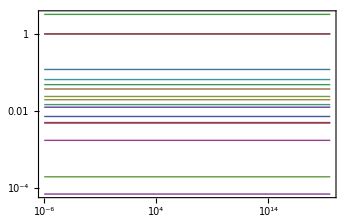

```mathematica
{concSol,fluxSol}=simulate[ppp];
plotSimulation[concSol]
```

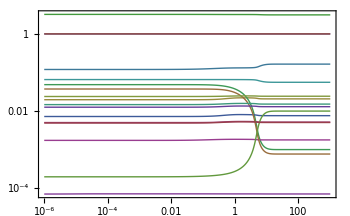

```mathematica
{concSol,fluxSol}=simulate[ppp,{t,0,1000},Parameters->{rateconst["vgshr", True]->46 Liter(Hour Mole)^-1}];
plotSimulation[concSol,{t,0,1000}]
```